```mathematica
ClearAll["global`*"]
```

## Initialization

### Solution in external harmonic potential

```mathematica
M={{-(κ+k)/γ,κ/γ},{κ/γ,-κ/γ}};
```

```mathematica
MatrixForm[M];
```

```mathematica
expM=MatrixExp[M*(-tp)];
```

```mathematica
covar=Integrate[expM.{{2*Subscript[T, c]/γ,0},{0,2*Subscript[T, h]/γ}}.Transpose[expM],{tp,-Infinity,0},Assumptions->{γ>0,k>0,κ>0}];
```

```mathematica
FullSimplify[covar/.{Subscript[T, c]->Subscript[T, h]},Assumptions->{γ>0,k>0,κ>0}];
```

```mathematica
P[x_,y_,kk_]:=Simplify[Exp[-1/2*{x,y}.Inverse[covar].{x,y}]]/.{k->kk};
```

```mathematica
Log[P[x,y,k]];
```

### Patching and normalization

```mathematica
SubMinus[k]=2*Subscript[U, 0]/L^2;
```

```mathematica
SubPlus[k]=2*Subscript[U, 0]/l^2;
```

```mathematica
SubMinus[f]=FullSimplify[Integrate[P[x,y,SubMinus[k]],{y,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
SubPlus[f]=FullSimplify[Integrate[P[x,y,SubPlus[k]],{y,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{x->0})==SubPlus[A]*(SubPlus[f]/.{x->0})&&SubMinus[A]*Integrate[SubMinus[f],{x,-L,0},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]+SubPlus[A]*Integrate[SubPlus[f],{x,0,l},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]==1,{SubMinus[A],SubPlus[A]}],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

{{A_-→(2 √2 U_0 (L^2 κ+U_0) √((κ (l^2 κ+U_0))/((l^2 κ T_h+T_c (l^2 κ+2 U_0)) (L^4 κ^2 T_c^2+L^4 κ^2 T_h^2+2 T_c T_h (L^4 κ^2+4 L^2 κ U_0+2 U_0^2)))))/(l L π (Erf[√2 √((U_0 (L^2 κ+U_0))/(L^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (l^2 κ+U_0))/(l^4 κ T_h+T_c (l^4 κ+2 l^2 U_0)))+Erf[√2 √((U_0 (l^2 κ+U_0))/(l^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (L^2 κ+U_0))/(L^4 κ T_h+T_c (L^4 κ+2 L^2 U_0))))),A_+→(2 √2 U_0 (l^2 κ+U_0) √((κ (L^2 κ+U_0))/((L^2 κ T_h+T_c (L^2 κ+2 U_0)) (l^4 κ^2 T_c^2+l^4 κ^2 T_h^2+2 T_c T_h (l^4 κ^2+4 l^2 κ U_0+2 U_0^2)))))/(l L π (Erf[√2 √((U_0 (L^2 κ+U_0))/(L^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (l^2 κ+U_0))/(l^4 κ T_h+T_c (l^4 κ+2 l^2 U_0)))+Erf[√2 √((U_0 (l^2 κ+U_0))/(l^2 κ (T_c+T_h)+2 T_c U_0))] √((U_0 (L^2 κ+U_0))/(L^4 κ T_h+T_c (L^4 κ+2 L^2 U_0)))))}}

## Current density maps

```mathematica
Subscript[p, left]=Simplify[((SubMinus[A]/. SubMinus[exprA])* P[x,y,SubMinus[k]]/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2})/.{d->1,Subscript[U, 0]->1,γ->1},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
Subscript[p, right]=Simplify[((SubPlus[A]/. SubPlus[exprA])* P[x,y,SubPlus[k]]/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2})/.{d->1,Subscript[U, 0]->1,γ->1},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
prob = Piecewise[{{Subscript[p, left],x≤0},{Subscript[p, right],x>0}}];
```

```mathematica
probs = prob/.{y->-s+x};
```

```mathematica
probs = probs/.{x->x-Subscript[λ, l]};
```

```mathematica
probs = probs/.{x->1-x};
```

```mathematica
Subscript[T, choose]= 0.1
```

0.1

```mathematica
probplot = probs/.{s->s,x->x,Subscript[λ, l]->0.3,Subscript[λ, r]->0.7,κ->1,Subscript[T, 1]->Subscript[T, choose],Subscript[T, 2]->1.0};
```

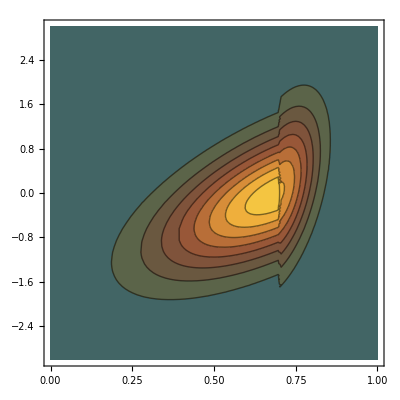

```mathematica
ContourPlot[probplot,{x,0,1},{s,-3,3},PlotRange->{{0,1},{-3,3},{0,3.5}},Exclusions->None,ColorFunction->"Autumn",Contours->20]
```

```mathematica
loopypot = Piecewise[{{Mod[x,1]^2/(Subscript[λ, l]^2),Mod[x,1]<Subscript[λ, l]},{(Mod[x,1]-1)^2/(Subscript[λ, r]^2),Mod[x,1]>Subscript[λ, l]}}];
```

```mathematica
gpot = D[loopypot,x]/.{x->x+Subscript[λ, l]};
```

```mathematica
jx =-probs*((gpot)-s*κ)-Subscript[T, 1]*D[probs,{x,1}]-Subscript[T, 1]*D[probs,{s,1}];
js = (probs*((gpot)-2*κ*s))-Subscript[T, 1]*D[probs,{x,1}]-(Subscript[T, 1]+Subscript[T, 2])*D[probs,{s,1}];
```

```mathematica
jcurl = Curl[{jx,js},{x,s}];
```

```mathematica
jxplot = jx/.{Subscript[λ, l]->0.3,Subscript[λ, r]->0.7,κ->1,Subscript[T, 1]->Subscript[T, choose],Subscript[T, 2]->1.0};
jsplot = js/.{Subscript[λ, l]->0.3,Subscript[λ, r]->0.7,κ->1,Subscript[T, 1]->Subscript[T, choose],Subscript[T, 2]->1.0};
```

```mathematica
jcplot = jcurl/.{Subscript[λ, l]->0.3,Subscript[λ, r]->0.7,κ->1,Subscript[T, 1]->Subscript[T, choose],Subscript[T, 2]->1.0};
```

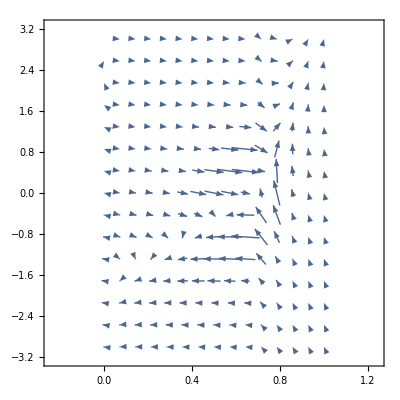

```mathematica
VectorPlot[1*{jxplot,jsplot},{x,0,1},{s,-3,3},VectorScale->{Medium,1/6,Automatic}]
```

```mathematica
mvx = MinValue[jxplot,{x,s}];
```

```mathematica
mxvx = MaxValue[jxplot,{x,s}];
```

```mathematica
mvs = MinValue[jsplot,{x,s}];
```

```mathematica
mxvs = MaxValue[jsplot,{x,s}];
```

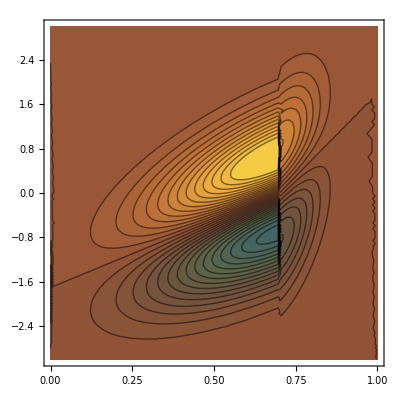

```mathematica
ContourPlot[1*jxplot,{x,0,1},{s,-3,3},PlotRange->{{0,1},{-3,3},{-1,mxvx}},Exclusions->None,Contours->50,ColorFunction->"Autumn"]
```

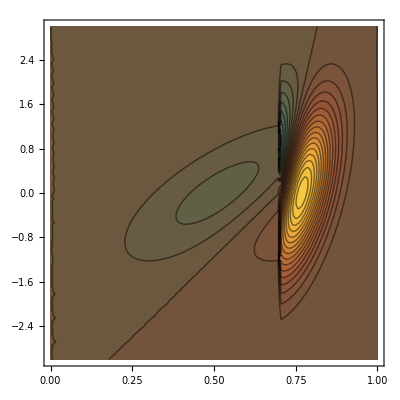

```mathematica
ContourPlot[1*jsplot,{x,0,1},{s,-3,3},PlotRange->{{0,1},{-3,3},{-2,3}},Exclusions->None,Contours->50,ColorFunction->"Autumn"]
```

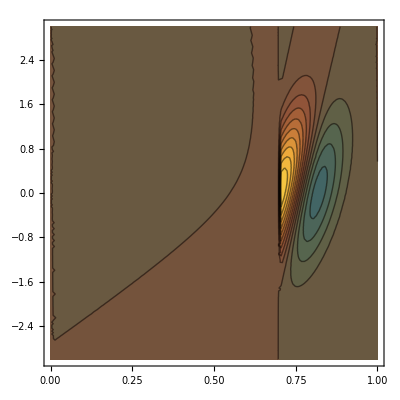

```mathematica
ContourPlot[1*jcplot,{x,0,1},{s,-3,3},PlotRange->{{0,1},{-3,3},{-100,100}},Exclusions->None,Contours->50,ColorFunction->"Autumn"]
```

```mathematica
Plot[{1*jxplot/.{s->0},1*jsplot/.{s->0}},{x,0,1},PlotRange->All]
```

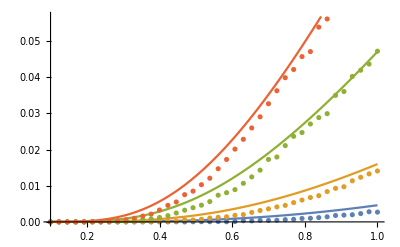
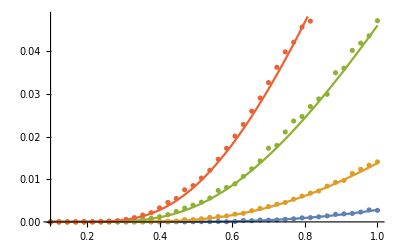
```mathematica
Current
Subscript[J, R] = Simplify[-(k*x+κ*(x-y))/γ*P[x,y,k]-Subscript[T, c]/γ*D[P[x,y,k],x],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
-(ⅇ^(-((k+2 κ) (κ (k y^2+(x-y)^2 κ) Subscript[T, c]+(k^2 x^2+k x (3 x-2 y) κ+(x-y)^2 κ^2) Subscript[T, h]))/(2 (κ^2 Subscript[T, c]^2+(k^2+4 k κ+2 κ^2) Subscript[T, c] Subscript[T, h]+κ^2 Subscript[T, h]^2))) κ^2 (Subscript[T, c]-Subscript[T, h]) ((k y+(-x+y) κ) Subscript[T, c]-(k x+(x-y) κ) Subscript[T, h]))/(γ (κ^2 Subscript[T, c]^2+(k^2+4 k κ+2 κ^2) Subscript[T, c] Subscript[T, h]+κ^2 Subscript[T, h]^2))
{{SubPlus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/.{x->l,k->SubPlus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
Solve::ifun: "Inverse functions are being used by \!\(\*RowBox[{\"Solve\"}]\), so some solutions may not be found; use Reduce for complete solution information."
{{SubMinus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/.{x->-L,k->SubMinus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
Solve::ifun: "Inverse functions are being used by \!\(\*RowBox[{\"Solve\"}]\), so some solutions may not be found; use Reduce for complete solution information."
{{y->-(L^3 κ (Subscript[T, c]+Subscript[T, h])+2 L Subscript[T, h] Subscript[U, 0])/(L^2 κ (Subscript[T, c]+Subscript[T, h])+2 Subscript[T, c] Subscript[U, 0])}}
Subscript[J, right]=Simplify[Integrate[SubPlus[A]*Subscript[J, R]/.{x->l,k->SubPlus[k],SubPlus[exprA]},{y,y/.{SubPlus[exprr]},Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
Subscript[J, left]=Simplify[Integrate[SubMinus[A]*Subscript[J, R]/.{x->-L,k->SubMinus[k],SubMinus[exprA]},{y,-Infinity,y/.{SubMinus[exprr]}},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
Subscript[J, total]= Simplify[Subscript[J, right]+Subscript[J, left],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
Subscript[J, unitless]=Simplify[ Subscript[J, total]/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
Subscript[J, paper]= Simplify[Subscript[J, unitless]/.{Subscript[T, 1]->T*(1-δ),Subscript[T, 2]->T*(1+δ)},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,T>0,δ>0,d>0}];
Subscript[J, exp]= Simplify[Subscript[J, paper]/.{κ->q*T},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
Subscript[J, sub]=Simplify[Subscript[J, unitless]/.{Subscript[U, 0]->1,d->1,Subscript[λ, l]->0.1,Subscript[λ, r]->0.9,γ->1},{κ>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
Subscript[J, subz]= 1/2*Subscript[J, sub]/.{Subscript[T, 1]->0,Subscript[T, 2]->T};
Subscript[J, subn]=1/2*Subscript[J, sub]/.{Subscript[T, 1]->0.1,Subscript[T, 2]->T};
v1 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k1_t0.h5","vvals"];
v2 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k2_t0.h5","vvals"];
v5 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k5_t0.h5","vvals"];
v10 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k10_t0.h5","vvals"];
tvals = Array[# & ,40, {0.1,1}]
{0.1,0.12307692307692308,0.14615384615384616,0.16923076923076924,0.19230769230769232,0.2153846153846154,0.23846153846153847,0.26153846153846155,0.2846153846153846,0.3076923076923077,0.3307692307692308,0.3538461538461538,0.3769230769230769,0.4,0.42307692307692313,0.4461538461538461,0.46923076923076923,0.49230769230769234,0.5153846153846154,0.5384615384615384,0.5615384615384615,0.5846153846153846,0.6076923076923076,0.6307692307692307,0.6538461538461539,0.676923076923077,0.7000000000000001,0.7230769230769231,0.7461538461538462,0.7692307692307693,0.7923076923076923,0.8153846153846154,0.8384615384615385,0.8615384615384616,0.8846153846153847,0.9076923076923077,0.9307692307692308,0.9538461538461539,0.9769230769230769,1.}
Show[{Plot[{Subscript[J, subn]/.{κ->1},Subscript[J, subn]/.{κ->2},Subscript[J, subn]/.{κ->5},Subscript[J, subn]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1},Transpose@{tvals,-v2},Transpose@{tvals,-v5},Transpose@{tvals,-v10}}]}]
-Graphics-
Show[{Plot[{Subscript[J, subn2]/.{κ->1},Subscript[J, subn2]/.{κ->2},Subscript[J, subn2]/.{κ->5},Subscript[J, subn2]/.{κ->10}},{T,0.1,1}]}]
-Graphics-
v1t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k1_t0.h5","vvals"];
v2t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k2_t0.h5","vvals"];
v5t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k5_t0.h5","vvals"];
v10t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k10_t0.h5","vvals"];
Show[{Plot[{Subscript[J, subz]/.{κ->1},Subscript[J, subz]/.{κ->2},Subscript[J, subz]/.{κ->5},Subscript[J, subz]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1t0},Transpose@{tvals,-v2t0},Transpose@{tvals,-v5t0},Transpose@{tvals,-v10t0}}]}]
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"409994.71954227815`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"407994.469307536`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"407981.55034613627`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"General\", \"::\", \"munfl\"}], \"MessageName\"]\) will be suppressed during this calculation."
-Graphics-
```

## Current

```mathematica
Subscript[J, R] = Simplify[-(k*x+κ*(x-y))/γ*P[x,y,k]-Subscript[T, c]/γ*D[P[x,y,k],x],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

-(ⅇ^(-((k+2 κ) (κ (k y^2+(x-y)^2 κ) T_c+(k^2 x^2+k x (3 x-2 y) κ+(x-y)^2 κ^2) T_h))/(2 (κ^2 T_c^2+(k^2+4 k κ+2 κ^2) T_c T_h+κ^2 T_h^2))) κ^2 (T_c-T_h) ((k y+(-x+y) κ) T_c-(k x+(x-y) κ) T_h))/(γ (κ^2 T_c^2+(k^2+4 k κ+2 κ^2) T_c T_h+κ^2 T_h^2))

```mathematica
{{SubPlus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/.{x->l,k->SubPlus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{SubMinus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/.{x->-L,k->SubMinus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→-(L^3 κ (T_c+T_h)+2 L T_h U_0)/(L^2 κ (T_c+T_h)+2 T_c U_0)}}

```mathematica
Subscript[J, right]=Simplify[Integrate[SubPlus[A]*Subscript[J, R]/.{x->l,k->SubPlus[k],SubPlus[exprA]},{y,y/.{SubPlus[exprr]},Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, left]=Simplify[Integrate[SubMinus[A]*Subscript[J, R]/.{x->-L,k->SubMinus[k],SubMinus[exprA]},{y,-Infinity,y/.{SubMinus[exprr]}},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, total]= Simplify[Subscript[J, right]+Subscript[J, left],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, unitless]=Simplify[ Subscript[J, total]/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
Subscript[J, paper]= Simplify[Subscript[J, unitless]/.{Subscript[T, 1]->T*(1-δ),Subscript[T, 2]->T*(1+δ)},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,T>0,δ>0,d>0}];
```

```mathematica
Subscript[J, exp]= Simplify[Subscript[J, paper]/.{κ->q*T},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
Subscript[J, sub]=Simplify[Subscript[J, unitless]/.{Subscript[U, 0]->1,d->1,Subscript[λ, l]->0.1,Subscript[λ, r]->0.9,γ->1},{κ>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
Subscript[J, subz]= 1/2*Subscript[J, sub]/.{Subscript[T, 1]->0,Subscript[T, 2]->T};
Subscript[J, subn]=1/2*Subscript[J, sub]/.{Subscript[T, 1]->0.1,Subscript[T, 2]->T,κ->κ};
```

```mathematica
v1 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k1.h5","vvals"];
```

```mathematica
v2 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k2.h5","vvals"];
```

```mathematica
v5 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k5.h5","vvals"];
```

```mathematica
v10 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k10.h5","vvals"];
```

```mathematica
tvals = Array[# & ,40, {0.1,1}]
```

{0.1,0.123077,0.146154,0.169231,0.192308,0.215385,0.238462,0.261538,0.284615,0.307692,0.330769,0.353846,0.376923,0.4,0.423077,0.446154,0.469231,0.492308,0.515385,0.538462,0.561538,0.584615,0.607692,0.630769,0.653846,0.676923,0.7,0.723077,0.746154,0.769231,0.792308,0.815385,0.838462,0.861538,0.884615,0.907692,0.930769,0.953846,0.976923,1.}

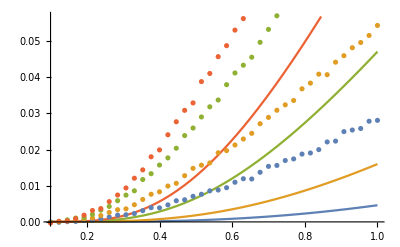

```mathematica
Show[{Plot[{Subscript[J, subn]/.{κ->1},Subscript[J, subn]/.{κ->2},Subscript[J, subn]/.{κ->5},Subscript[J, subn]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1},Transpose@{tvals,-v2},Transpose@{tvals,-v5},Transpose@{tvals,-v10}}]}]
```

```mathematica
v1t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k1_t0.h5","vvals"];
```

```mathematica
v2t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k2_t0.h5","vvals"];
```

```mathematica
v5t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k5_t0.h5","vvals"];
```

```mathematica
v10t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k10_t0.h5","vvals"];
```

```mathematica
Show[{Plot[{Subscript[J, subz]/.{κ->1},Subscript[J, subz]/.{κ->2},Subscript[J, subz]/.{κ->5},Subscript[J, subz]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1t0},Transpose@{tvals,-v2t0},Transpose@{tvals,-v5t0},Transpose@{tvals,-v10t0}}]}]
```

General::munfl: Exp[-409995.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-407994.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-407982.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

## Corrections

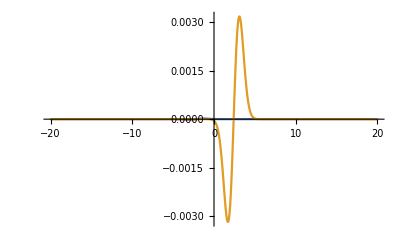

```mathematica
Plot[{(SubMinus[A]*Subscript[J, R]/.{x->-L,k->SubMinus[k],SubMinus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, c]->0.1,Subscript[T, h]->1,κ->1,L->0.3,l->0.7},(SubPlus[A]*Subscript[J, R]/.{x->l,k->SubPlus[k],SubPlus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, c]->0.1,Subscript[T, h]->1,κ->1,L->0.3,l->0.7}},{y,-20,20},PlotRange->All]
```

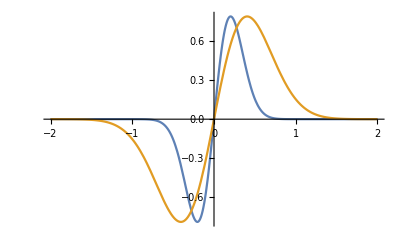

```mathematica
Plot[{(SubMinus[A]*Subscript[J, R]/.{x->0,k->SubMinus[k],SubMinus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, c]->0.,Subscript[T, h]->1,κ->1,L->0.3,l->0.7},(SubPlus[A]*Subscript[J, R]/.{x->0.000,k->SubPlus[k],SubPlus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, c]->0.,Subscript[T, h]->1,κ->1,L->0.3,l->0.7}},{y,-2,2},PlotRange->All]
```

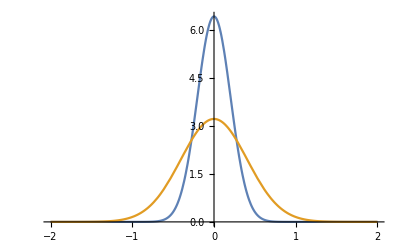

```mathematica
Plot[{(SubMinus[A]*P[x,y,k]/.{x->0,k->SubMinus[k],SubMinus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, c]->0.,Subscript[T, h]->1,κ->1,L->0.3,l->0.7},(SubPlus[A]*P[x,y,k]/.{x->0,k->SubPlus[k],SubPlus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, c]->0.,Subscript[T, h]->1,κ->1,L->0.3,l->0.7}},{y,-2,2}]
```

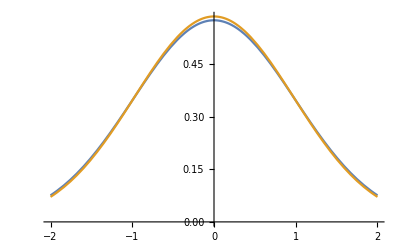

```mathematica
Plot[{(SubMinus[A]*P[x,y,k]/.{x->0,k->SubMinus[k],SubMinus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, c]->0.75,Subscript[T, h]->1,κ->1,L->0.3,l->0.7},(SubPlus[A]*P[x,y,k]/.{x->0,k->SubPlus[k],SubPlus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, c]->0.75,Subscript[T, h]->1,κ->1,L->0.3,l->0.7}},{y,-2,2}]
```

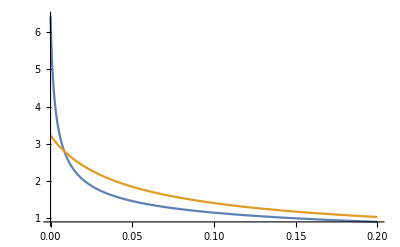

```mathematica
Plot[{(SubMinus[A]*P[0,0,SubMinus[k]]/.{SubMinus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, h]->1,κ->1,L->0.3,l->0.7},(SubPlus[A]*P[0,0,SubPlus[k]]/.{SubPlus[exprA]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, h]->1,κ->1,L->0.3,l->0.7}},{Subscript[T, c],0,0.2},PlotRange->All]
```

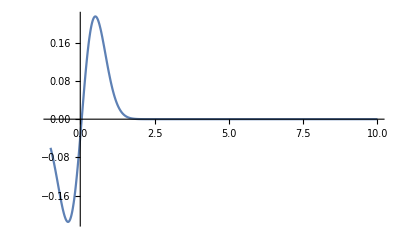

```mathematica
Plot[(Subscript[J, R]/.{x->0.01,k->SubPlus[k]})/.{γ->1,Subscript[U, 0]->1,Subscript[T, c]->0.01,Subscript[T, h]->1,κ->1,l->0.7},{y,-1,10},PlotRange->All]
```

```mathematica
Subscript[J, R2]= FullSimplify[Subscript[J, R]/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, h]>Subscript[T, c]>0,d>0}]/.{Subscript[U, 0]->1,γ->1,d->1}
```

(ⅇ^(-((k+2 κ) (k^2 x^2 T_2+(x-y)^2 κ^2 (T_1+T_2)+k κ (y^2 T_1+x (3 x-2 y) T_2)))/(2 (k^2 T_1 T_2+4 k κ T_1 T_2+κ^2 (T_1+T_2)^2))) κ^2 (-k (T_1-T_2) (y T_1-x T_2)+(x-y) κ (T_1^2-T_2^2)))/(k^2 T_1 T_2+4 k κ T_1 T_2+κ^2 (T_1+T_2)^2)

```mathematica
SubPlus[r]= FullSimplify[(y/.{SubPlus[exprr]})/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, h]>Subscript[T, c]>0,d>0}]/.{Subscript[U, 0]->1,γ->1,d->1}
```

(2 T_2 λ_r+κ (T_1+T_2) λ_r^3)/(2 T_1+κ (T_1+T_2) λ_r^2)

```mathematica
SubPlus[k]= FullSimplify[(SubPlus[k])/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, h]>Subscript[T, c]>0,d>0}]/.{Subscript[U, 0]->1,γ->1,d->1}
```

2/λ_r^2

```mathematica
Subscript[J, rdy]=Simplify[Series[(Subscript[J, R2]/.{x->{x+δ}})/.{x->Subscript[λ, r],y->SubPlus[r],k->SubPlus[k]},{ϵ,0,1}],Assumptions->{κ>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, 1]>Subscript[T, 2]>0}]
```

J_R2

```mathematica
FullSimplify[Series[Subscript[J, rdy],{Subscript[T, 1],0,2}],Assumptions->{κ>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, 1]>Subscript[T, 2]>0}]
```

(-ⅇ^(-(2 (1+1/(κ λ_r^2)))/T_2) κ+(2 ⅇ^(-(2 (1+1/(κ λ_r^2)))/T_2) (-1+T_2) (1+κ λ_r^2) (2+κ λ_r^2) T_1)/(κ T_2^2 λ_r^4)+(2 ⅇ^(-(2 (1+1/(κ λ_r^2)))/T_2) (1+κ λ_r^2) (-(1+κ λ_r^2) (2+κ λ_r^2)^2+T_2 (2+κ λ_r^2)^2 (2+3 κ λ_r^2)-T_2^2 (8+κ λ_r^2 (2+κ λ_r^2) (10+κ λ_r^2))) T_1^2)/(κ^3 T_2^4 λ_r^8)+O[T_1]^3) ϵ+O[ϵ]^2

```mathematica
dp =FullSimplify[D[Subscript[J, rdy],δ]/.{δ->0},Assumptions->{κ>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, 1]>Subscript[T, 2]>0}]
```

{(ⅇ^(-(2 (1+κ λ_r^2))/(2 T_1+κ (T_1+T_2) λ_r^2)) κ^2 (T_1-T_2) λ_r^2 (2 T_2+κ (T_1+T_2) λ_r^2))/(4 T_1 T_2+8 κ T_1 T_2 λ_r^2+κ^2 (T_1+T_2)^2 λ_r^4)+(4 ⅇ^(-(2 (1+κ λ_r^2))/(2 T_1+κ (T_1+T_2) λ_r^2)) κ^2 (-T_1+T_2) λ_r (1+κ λ_r^2) ϵ)/(4 T_1 T_2+8 κ T_1 T_2 λ_r^2+κ^2 (T_1+T_2)^2 λ_r^4)+O[ϵ]^2}

```mathematica
FullSimplify[Limit[dp,{Subscript[T, 1]->0}],Assumptions->{κ>0,Subscript[λ, l]>0,Subscript[λ, r]>0,Subscript[T, 1]>Subscript[T, 2]>0}]
```

{(ⅇ^(-(2 (1+1/(κ λ_r^2)))/T_2) (-T_2 λ_r (2+κ λ_r^2)+4 (ϵ+ϵ κ λ_r^2)))/(T_2 λ_r^3)}